```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
region={{0,0},{1,0},{1,1},{0,1}};
jump={{.2,.2},{.8,.2},{.8,.8},{.2,.8}};
f1={{0,.9},{.1,.9},{.1,1}};
f2={{1,.1},{.9,.1},{.9,0}};
```

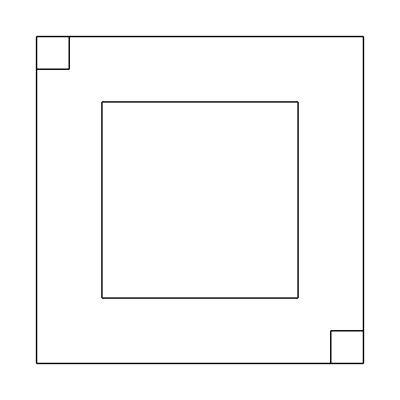

```mathematica
bMesh=ToBoundaryMesh["Coordinates"-> Join[region,jump,f1,f2],"BoundaryElements"->LineElement/@{
{{1,2},{2,3},{3,4},{4,1}},
{{5,6},{6,7},{7,8},{8,5}},
{{9,10},{10,11}},
{{12,13},{13,14}}
}];
bMesh["Wireframe"]
```

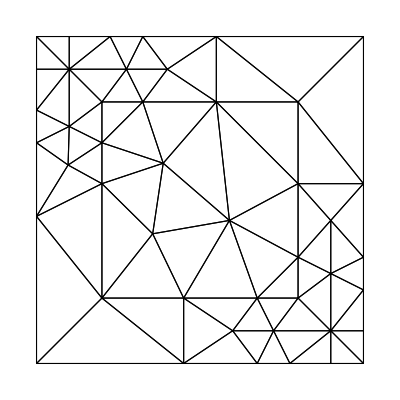

```mathematica
eMesh=ToElementMesh[bMesh,"MeshOrder"->1,"MaxCellMeasure"->∞];
eMesh["Wireframe"]
```

```mathematica
mesh=create𝒯fromElementMesh@eMesh;
SetDirectory@NotebookDirectory[];
export[mesh,"jmp_mesh",<|"format"->"NT"|>]
```

jmp_mesh.nt